```mathematica
(* Calculate the slope of Theta(ks), and find the curvature corresponding to integer ks*)
```

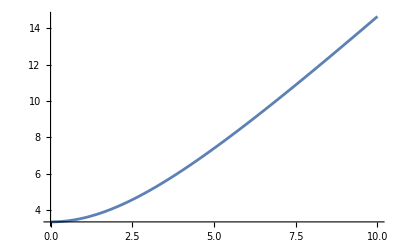

```mathematica
(* Define Theta(ks)=2*Psi(a=atot). *)
Clear[a, ks, kc,PsiIntCurved, Theta, DTheta]
PsiIntCurved[a_,ks_,kc_]:=(ks^2+8*kc)^0.5*(kc-(kc^2-1)^0.5)^0.5*(EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2+6*kc)-((ks^2+6*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2]-EllipticPi[-1/2*(kc-(kc^2-1)^0.5)*((ks^2+6*kc)+((ks^2+6*kc)^2-4)^0.5),ArcSin[a/(kc-(kc^2-1)^0.5)^0.5],((kc^2-1)^0.5-kc)^2]);
(*Note: atot[kc_] := (kc-(kc^2-1)^0.5)^0.5; for kc<1
atot[kc_]=1 for kc>1 *)
Theta[ks_, kc_]:=2*PsiIntCurved[a, ks, kc]/.{a->Max[1,Re[(kc-(kc^2-1)^0.5)^0.5]]};
Plot[{Re[Theta[ks,kc]]/.{kc->2}},{ks,0,10}]
```

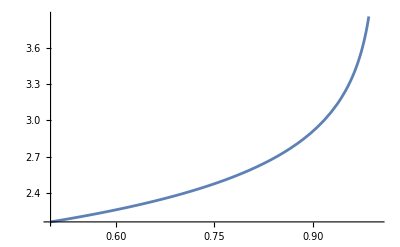

```mathematica
(* Define slope of Theta(ks) as its derivative w.r.t. ks *)
DTheta[ks_,kc_]:=Derivative[1,0][Theta][ks,kc];
Plot[Re[DTheta[ks,kc]]/.{ks->1000},{kc,0.5,0.999}]
```

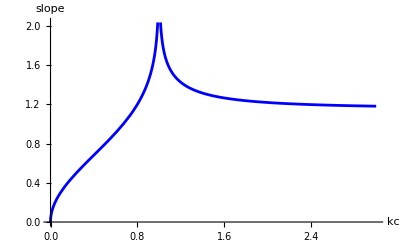

```mathematica
(* Define the transformation constant for the slope *)
Clear[kc, K,OmegaK,a0bar,kTransConstant,DThetakc,TransSlope]
H0=2.2685455026110553*10^-18 ; (*SI value*)
c=2.99792458*10^8;(*SI value*)
h=0.7;
Omegalambda=0.679;
Omegarh2=4.53*10^-5;
Omegar=Omegarh2/h^2;
Lambda=Omegalambda*3*H0^2/c^2;
a0=(Omegalambda/Omegar)^0.25;

K[kc_]:=2.*Lambda/3.*kc;
OmegaK[kc_]:=-K[kc]*c^2/a0^2/H0^2;
a0bar[kc_]:=c*(-1/OmegaK[kc])^0.5/H0;
kTransConstant[kc_]:=a0/a0bar[kc]/Lambda^0.5;
(* Define slope of Theta(ks) as its derivative w.r.t. ks, with ks large (1000) *)
DThetakc[kc_]:=Re[DTheta[ks,kc]]/.{ks->1000};
(* Define the slope after transformation *)
TransSlope[kc_]:=2/π* DThetakc[kc]*kTransConstant[kc];
Plot[TransSlope[kc],{kc,0,3}, AxesLabel->{kc,"slope"}, PlotStyle->Blue]
```

OmegaK

{{kc→0.113284},{kc→0.238231},{kc→0.671658},{kc→1.01526},{kc→0.99969}}

{-0.00179508,-0.00377498,-0.010643,-0.0160877,-0.015841}

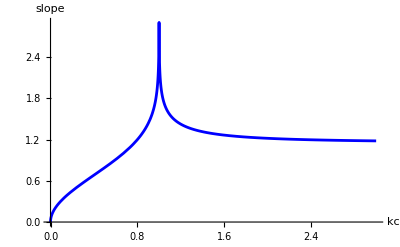

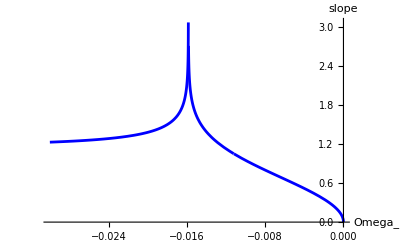

```mathematica
Clear[kc,SlopeValues,initialGuess,kcRoots,kcSolutions,kcInv]
(*Define the set of slope values*)
SlopeValues={1/3,1/2,1,2,3};
(*Find the corresponding kc values numerically*)
initialGuess=0.6; (*Adjust the initial guess as needed*)OmegaK
kcRoots=Table[FindRoot[TransSlope[kc]==slopeVal,{kc,initialGuess}],{slopeVal,SlopeValues}]
(*OmegaKSolutions = {N[NumberForm[OmegaK[kc/.kcSolutions[[1]]],4]],N[NumberForm[ OmegaK[kc/.kcSolutions[[2]]],4]],N[NumberForm[OmegaK[kc/.kcSolutions[[3]]],4]],N[NumberForm[OmegaK[kc/.kcSolutions[[4]]],4]],N[NumberForm[OmegaK[kc/.kcSolutions[[5]]],4]]};*)
kcSolutions= {kc/.kcRoots[[1]],kc/.kcRoots[[2]],kc/.kcRoots[[3]],kc/.kcRoots[[4]],kc/.kcRoots[[5]]};
OmegaKSolutions = {OmegaK[kcSolutions[[1]]],OmegaK[kcSolutions[[2]]],OmegaK[kcSolutions[[3]]],OmegaK[kcSolutions[[4]]],OmegaK[kcSolutions[[5]]]}
(*Plot the slope with the discrete kc solutions*)
kcInv[omegaK_]:=InverseFunction[OmegaK][omegaK];
Plot[TransSlope[kc],{kc,0,3}, AxesLabel->{kc,"slope"},PlotRange->All,PlotStyle->Blue,GridLines->{kcSolutions,SlopeValues}]
Plot[TransSlope[kcInv[omegaK]],{omegaK,0,-0.03},PlotRange->All, PlotStyle->Blue, AxesLabel->{Omega_K,slope},GridLines->{OmegaKSolutions,SlopeValues}]
```

```mathematica
Clear[plt]
plot=Plot[TransSlope[kcInv[omegaK]],
{omegaK,0,-0.03}, PlotRange->{{0,-0.03},{0,3.1}},ImageSize->500,Epilog->{Directive[Black,Dashed],Line[{{0.0,SlopeValues[[2]]},{OmegaKSolutions[[2]],SlopeValues[[2]]}}],Line[{{0.0,SlopeValues[[3]]},{OmegaKSolutions[[3]],SlopeValues[[3]]}}],Line[{{0.0,SlopeValues[[4]]},{OmegaKSolutions[[4]],SlopeValues[[4]]}}],Line[{{0.0,SlopeValues[[5]]},{OmegaKSolutions[[5]],SlopeValues[[5]]}}],Line[{{OmegaKSolutions[[2]],0},{OmegaKSolutions[[2]],SlopeValues[[2]]}}],Line[{{OmegaKSolutions[[3]],0},{OmegaKSolutions[[3]],SlopeValues[[3]]}}],Line[{{OmegaKSolutions[[4]],0},{OmegaKSolutions[[4]],SlopeValues[[4]]}}],Line[{{OmegaKSolutions[[5]],0},{OmegaKSolutions[[5]],SlopeValues[[5]]}}]}, AspectRatio->2/3,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.005], FontSize->15], FrameTicks->{{None,{SlopeValues[[2]],SlopeValues[[3]],SlopeValues[[4]],SlopeValues[[5]]}},{{-0.0038,-0.0106,-0.0160},None}},FrameLabel->{Style["Ω_(κ, 0)", FontSize->20,FontFamily->"Times"],Style["2/πdθ/dk (Slope)",FontSize->20,FontFamily->"Times"]}
]
Export["kc-Slope.pdf",plot]
```

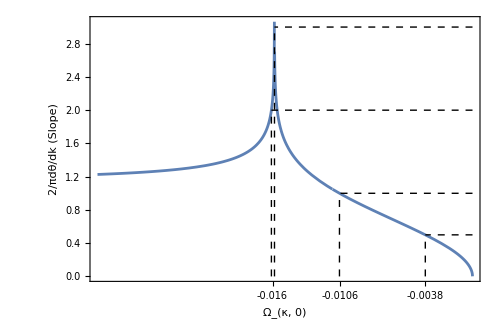

kc-Slope.pdf